# EIWL Sections 45 and 46

## 8/8 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

# Chapter 45

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Tue 1 Jul 2025. Please

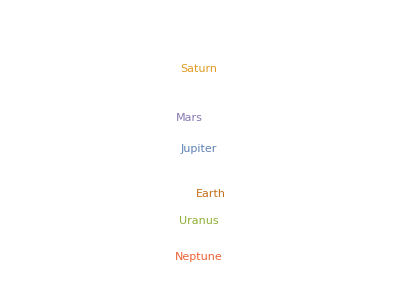

```mathematica
planets=CloudGet["https://wolfr.am/7FxLgPm5"];
WordCloud[Normal[planets[All,"Moons",Length]]]
```

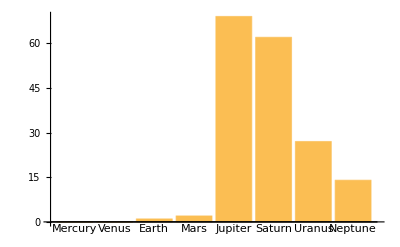

```mathematica
BarChart[planets[All,"Moons",Length],ChartLabels->Automatic]
```

```mathematica
SortBy[planets[All,"Mass"],planets[All,"Moons",Length]]
```

```mathematica
planets[All,"Moons", Max,"Mass"]
```

```mathematica
SortBy[planets[All,"Moons", Total,"Mass"],planets[All,"Moons", Max,"Mass"]]
```

```mathematica
planets[All,"Moons",Median,"Mass"]
```

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]][All,Keys]
```

```mathematica
fireballs=ResourceData["Fireballs and Bolides"];
fireballs[Max,"Altitude"]
```

66.6 km

```mathematica
fireballs[TakeLargest[5],"Altitude"]
```

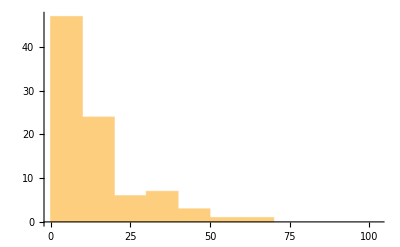

```mathematica
Histogram[Differences[fireballs[All,"PeakBrightness"]]]
```

```mathematica
GeoListPlot[fireballs[1;;10,"NearestCity"],GeoLabels->Automatic]
```

-Graphics-

```mathematica
GeoListPlot[fireballs[TakeLargestBy[#Altitude&,10],"NearestCity"],GeoLabels->Automatic]
```

-Graphics-

# Chapter 46

```mathematica
Spectrogram[SpeechSynthesize["123456"]]
```

-Graphics-

```mathematica
Spectrogram@SpeechSynthesize@Last@SortBy[WordList[],StringLength]
```

-Graphics-

```mathematica
SpeechSynthesize@StringRiffle@Alphabet[]
```

```mathematica
Spectrogram[SpeechSynthesize@StringRiffle@Alphabet[]]
```

-Graphics-

```mathematica
AudioPitchShift[SpeechSynthesize["hello"],2]
```

```mathematica
SpeechRecognize/@Table[AudioPitchShift[SpeechSynthesize["computer"],x],{x,1,1.5,0.1}]
```

{,,,,,}

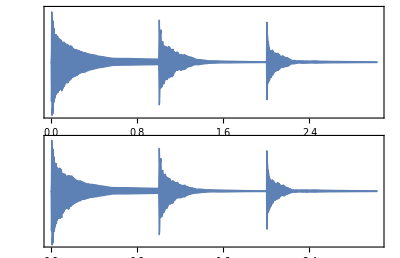

```mathematica
AudioPlot[Sound[Table[SoundNote[12x,1,"Guitar"],{x,3}]]]
```

```mathematica
AudioIdentify/@Table[AudioPitchShift[Sound[SoundNote[0,1,"Trumpet"]],x],{x,0.5,1,0.1}]
```

{trombone,trombone,trombone,trombone,trumpet,trumpet}

CurrentImage::nocam: Unable to connect to a camera. Check that a camera is properly connected and that it is not currently in use by another application.

Blur::imginv: Expecting an image or graphics instead of $Failed.

AnimationVideo[Blur[$Failed,20-t],{t,0,20}]

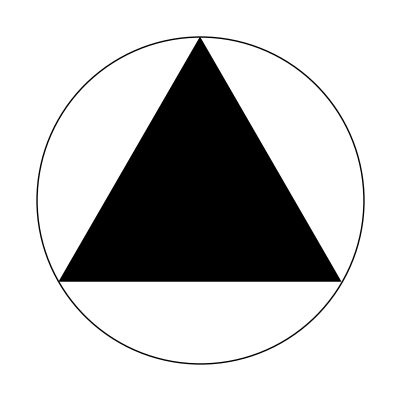

```mathematica
AnimationVideo[Blur[CurrentImage[],20-t],{t,0,20}]
```

```mathematica
AnimationVideo[Graphics[{Disk[],RegularPolygon[x]}],{x,3,20,1}]
```

AnimationVideo[-Graphics-,{x,3,20,1}]

```mathematica
AnimationVideo[Graphics[Style[Disk[],Hue[X]],50],{X,0,1}]
```

AnimationVideo[-Graphics-,{InterpolatingFunction[…],0,1}]

```mathematica
AnimationVideo[Rasterize[Style[ToUpperCase@FromLetterNumber[x],200]],{x,1,26,1}]
```

FromLetterNumber::nlst: The argument x is not an integer or a list of integers.

AnimationVideo[-Graphics-,{x,1,26,1}]